# PDE solver for the effective field theory of Dark Energy

## Farbod Hassani and Jean-Pierre Eckmann

Feb 2021

In this note book we convert a PDE to coupled ODEs and we try to solve them in a cosmological scheme.

## PDE to ODE example

```mathematica
Eq=Block[{pi},pi[t_,x_]:=assum[t,x];pde[t,x]]
```

pde[t,x]

```mathematica
For[i=1,i<6,i++,Print[ToString[x^i,StandardForm]<>": ",Coefficient[Eq,x^i]]]
```

x: 0

x^2: 0

x^3: 0

x^4: 0

x^5: 0

## Deriving the k-essence ODEs from the PDE

```mathematica
Clear[Eq,assum,pde];
```

#### PDE and assumptions

```mathematica
Ψ[τ_,x_]:=ψ0[τ]+ψ1[τ] x + ψ2[τ] x^2+ψ3[τ] x^3+ ψ4[τ] x^4;
assum[t_,x_] := Subscript[u, 0][t]+ Subscript[u, 1][t]x +  Subscript[u, 2][t] x^2+Subscript[u, 3][t] x^3+Subscript[u, 4][t] x^4;
L[τ_,x_] := Subscript[l, πd][τ]D[pi[τ,x], τ] + Subscript[l, ππ][τ]pi[τ,x]+Subscript[l, Ψ][τ] Ψ[τ,x]+Subscript[l, Ψd][τ] D[Ψ[τ,x], τ]+Subscript[l, πpp][τ]D[pi[τ,x], x,x];
NonLin[τ_,x_]:= Subscript[ν, πpπp][τ] (D[pi[τ,x], x])^2 +Subscript[ν, πpπpd][τ]D[pi[τ,x], x]D[pi[τ,x], τ,x] + 
Subscript[ν, ππpp][τ] pi[τ,x]D[pi[τ,x], x,x]+Subscript[ν, πdπpp][τ] D[pi[τ,x], τ] D[pi[τ,x], x,x]+
Subscript[ν, Ψπpp][τ] Ψ[τ,x] D[pi[τ,x], x,x]+Subscript[ν, Ψpπp][τ] D[Ψ[τ,x], x]D[pi[τ,x], x]+Subscript[ν, πpπpπpp][τ](D[pi[τ,x], x])^2 D[pi[τ,x], x,x];
Eq[t_,x_]:= D[pi[t,x], t,t]+1*L[t,x]-NonLin[t,x];
```

#### Print the equation

```mathematica
Print[Eq[τ,x]//pdConv]
```

-ν_πpπpd(τ) (∂pi(τ,x))/(∂x) (∂^2 pi(τ,x))/(∂τ ∂x)+l_πpp(τ) (∂^2 pi(τ,x))/(∂x^2)+l_πd(τ) (∂pi(τ,x))/(∂τ)+l_ππ(τ) pi(τ,x)-ν_πdπpp(τ) (∂pi(τ,x))/(∂τ) (∂^2 pi(τ,x))/(∂x^2)-ν_ππpp(τ) pi(τ,x) (∂^2 pi(τ,x))/(∂x^2)-ν_πpπpπpp(τ) (∂^2 pi(τ,x))/(∂x^2) ((∂pi(τ,x))/(∂x))^2-ν_Ψpπp(τ) (∂pi(τ,x))/(∂x) (4 x^3 ψ4(τ)+3 x^2 ψ1(τ) ψ2(τ)+3 x^2 ψ3(τ))-ν_Ψπpp(τ) (∂^2 pi(τ,x))/(∂x^2) (ψ0(τ)+x^4 ψ4(τ)+x^3 ψ1(τ) ψ2(τ)+x^3 ψ3(τ))-ν_πpπp(τ) ((∂pi(τ,x))/(∂x))^2+(∂^2 pi(τ,x))/(∂τ^2)+l_Ψ(τ) (ψ0(τ)+x^4 ψ4(τ)+x^3 ψ1(τ) ψ2(τ)+x^3 ψ3(τ))+l_Ψd(τ) ((∂ψ0(τ))/(∂τ)+x^4 (∂ψ4(τ))/(∂τ)+x^3 ψ1(τ) (∂ψ2(τ))/(∂τ)+x^3 ψ2(τ) (∂ψ1(τ))/(∂τ)+x^3 (∂ψ3(τ))/(∂τ))

```mathematica
NewEq=Block[{pi},pi[τ_,x_]:=assum[τ,x];Eq[τ,x]]
```

(ψ0[τ]+x^3 ψ1[τ] ψ2[τ]+x^3 ψ3[τ]+x^4 ψ4[τ]) l_Ψ[τ]+l_πpp[τ] (2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ])+l_ππ[τ] (u_0[τ]+x u_1[τ]+x^2 u_2[τ]+x^3 u_3[τ]+x^4 u_4[τ])-(u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ])^2 ν_πpπp[τ]-(2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) (u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ])^2 ν_πpπpπpp[τ]-(2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) (u_0[τ]+x u_1[τ]+x^2 u_2[τ]+x^3 u_3[τ]+x^4 u_4[τ]) ν_ππpp[τ]-(3 x^2 ψ1[τ] ψ2[τ]+3 x^2 ψ3[τ]+4 x^3 ψ4[τ]) (u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ]) ν_Ψpπp[τ]-(ψ0[τ]+x^3 ψ1[τ] ψ2[τ]+x^3 ψ3[τ]+x^4 ψ4[τ]) (2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) ν_Ψπpp[τ]+l_Ψd[τ] (ψ0'[τ]+x^3 ψ2[τ] ψ1'[τ]+x^3 ψ1[τ] ψ2'[τ]+x^3 ψ3'[τ]+x^4 ψ4'[τ])-(u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ]) ν_πpπpd[τ] (u_1'[τ]+2 x u_2'[τ]+3 x^2 u_3'[τ]+4 x^3 u_4'[τ])+l_πd[τ] (u_0'[τ]+x u_1'[τ]+x^2 u_2'[τ]+x^3 u_3'[τ]+x^4 u_4'[τ])-(2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) ν_πdπpp[τ] (u_0'[τ]+x u_1'[τ]+x^2 u_2'[τ]+x^3 u_3'[τ]+x^4 u_4'[τ])+u_0''[τ]+x u_1''[τ]+x^2 u_2''[τ]+x^3 u_3''[τ]+x^4 u_4''[τ]

```mathematica
For[i=0,i<5,i++,If[i==0, Print["x^0:"NewEq /.{x->0}]];If[i!=0,Print[ToString[x^i,StandardForm]<>": ",Coefficient[NewEq,x^i]]]]
```

x^0: (ψ0[τ] l_Ψ[τ]+l_ππ[τ] u_0[τ]+2 l_πpp[τ] u_2[τ]-u_1[τ]^2 ν_πpπp[τ]-2 u_1[τ]^2 u_2[τ] ν_πpπpπpp[τ]-2 u_0[τ] u_2[τ] ν_ππpp[τ]-2 ψ0[τ] u_2[τ] ν_Ψπpp[τ]+l_Ψd[τ] ψ0'[τ]+l_πd[τ] u_0'[τ]-2 u_2[τ] ν_πdπpp[τ] u_0'[τ]-u_1[τ] ν_πpπpd[τ] u_1'[τ]+u_0''[τ])

x: l_ππ[τ] u_1[τ]+6 l_πpp[τ] u_3[τ]-4 u_1[τ] u_2[τ] ν_πpπp[τ]-8 u_1[τ] u_2[τ]^2 ν_πpπpπpp[τ]-6 u_1[τ]^2 u_3[τ] ν_πpπpπpp[τ]-2 u_1[τ] u_2[τ] ν_ππpp[τ]-6 u_0[τ] u_3[τ] ν_ππpp[τ]-6 ψ0[τ] u_3[τ] ν_Ψπpp[τ]-6 u_3[τ] ν_πdπpp[τ] u_0'[τ]+l_πd[τ] u_1'[τ]-2 u_2[τ] ν_πdπpp[τ] u_1'[τ]-2 u_2[τ] ν_πpπpd[τ] u_1'[τ]-2 u_1[τ] ν_πpπpd[τ] u_2'[τ]+u_1''[τ]

x^2: l_ππ[τ] u_2[τ]+12 l_πpp[τ] u_4[τ]-4 u_2[τ]^2 ν_πpπp[τ]-6 u_1[τ] u_3[τ] ν_πpπp[τ]-8 u_2[τ]^3 ν_πpπpπpp[τ]-36 u_1[τ] u_2[τ] u_3[τ] ν_πpπpπpp[τ]-12 u_1[τ]^2 u_4[τ] ν_πpπpπpp[τ]-2 u_2[τ]^2 ν_ππpp[τ]-6 u_1[τ] u_3[τ] ν_ππpp[τ]-12 u_0[τ] u_4[τ] ν_ππpp[τ]-3 ψ1[τ] ψ2[τ] u_1[τ] ν_Ψpπp[τ]-3 ψ3[τ] u_1[τ] ν_Ψpπp[τ]-12 ψ0[τ] u_4[τ] ν_Ψπpp[τ]-12 u_4[τ] ν_πdπpp[τ] u_0'[τ]-6 u_3[τ] ν_πdπpp[τ] u_1'[τ]-3 u_3[τ] ν_πpπpd[τ] u_1'[τ]+l_πd[τ] u_2'[τ]-2 u_2[τ] ν_πdπpp[τ] u_2'[τ]-4 u_2[τ] ν_πpπpd[τ] u_2'[τ]-3 u_1[τ] ν_πpπpd[τ] u_3'[τ]+u_2''[τ]

x^3: ψ1[τ] ψ2[τ] l_Ψ[τ]+ψ3[τ] l_Ψ[τ]+l_ππ[τ] u_3[τ]-12 u_2[τ] u_3[τ] ν_πpπp[τ]-8 u_1[τ] u_4[τ] ν_πpπp[τ]-48 u_2[τ]^2 u_3[τ] ν_πpπpπpp[τ]-36 u_1[τ] u_3[τ]^2 ν_πpπpπpp[τ]-64 u_1[τ] u_2[τ] u_4[τ] ν_πpπpπpp[τ]-8 u_2[τ] u_3[τ] ν_ππpp[τ]-12 u_1[τ] u_4[τ] ν_ππpp[τ]-4 ψ4[τ] u_1[τ] ν_Ψpπp[τ]-6 ψ1[τ] ψ2[τ] u_2[τ] ν_Ψpπp[τ]-6 ψ3[τ] u_2[τ] ν_Ψpπp[τ]-2 ψ1[τ] ψ2[τ] u_2[τ] ν_Ψπpp[τ]-2 ψ3[τ] u_2[τ] ν_Ψπpp[τ]+ψ2[τ] l_Ψd[τ] ψ1'[τ]+ψ1[τ] l_Ψd[τ] ψ2'[τ]+l_Ψd[τ] ψ3'[τ]-12 u_4[τ] ν_πdπpp[τ] u_1'[τ]-4 u_4[τ] ν_πpπpd[τ] u_1'[τ]-6 u_3[τ] ν_πdπpp[τ] u_2'[τ]-6 u_3[τ] ν_πpπpd[τ] u_2'[τ]+l_πd[τ] u_3'[τ]-2 u_2[τ] ν_πdπpp[τ] u_3'[τ]-6 u_2[τ] ν_πpπpd[τ] u_3'[τ]-4 u_1[τ] ν_πpπpd[τ] u_4'[τ]+u_3''[τ]

x^4: ψ4[τ] l_Ψ[τ]+l_ππ[τ] u_4[τ]-9 u_3[τ]^2 ν_πpπp[τ]-16 u_2[τ] u_4[τ] ν_πpπp[τ]-90 u_2[τ] u_3[τ]^2 ν_πpπpπpp[τ]-80 u_2[τ]^2 u_4[τ] ν_πpπpπpp[τ]-120 u_1[τ] u_3[τ] u_4[τ] ν_πpπpπpp[τ]-6 u_3[τ]^2 ν_ππpp[τ]-14 u_2[τ] u_4[τ] ν_ππpp[τ]-8 ψ4[τ] u_2[τ] ν_Ψpπp[τ]-9 ψ1[τ] ψ2[τ] u_3[τ] ν_Ψpπp[τ]-9 ψ3[τ] u_3[τ] ν_Ψpπp[τ]-2 ψ4[τ] u_2[τ] ν_Ψπpp[τ]-6 ψ1[τ] ψ2[τ] u_3[τ] ν_Ψπpp[τ]-6 ψ3[τ] u_3[τ] ν_Ψπpp[τ]+l_Ψd[τ] ψ4'[τ]-12 u_4[τ] ν_πdπpp[τ] u_2'[τ]-8 u_4[τ] ν_πpπpd[τ] u_2'[τ]-6 u_3[τ] ν_πdπpp[τ] u_3'[τ]-9 u_3[τ] ν_πpπpd[τ] u_3'[τ]+l_πd[τ] u_4'[τ]-2 u_2[τ] ν_πdπpp[τ] u_4'[τ]-8 u_2[τ] ν_πpπpd[τ] u_4'[τ]+u_4''[τ]

ODEs are accesible by ODEs[i] where i is the exponent of x^i

```mathematica
For[i=0,i<5,i++,If[i==0, ODEs[i] =NewEq /.{x->0}] ;If[i!=0,ODEs[i] = Coefficient[NewEq,x^i]]];
```

## Cosmology calculator

```mathematica
pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

-Graphics-

```mathematica
(*scale factor as a function of the Redshift *)
scalfactor[z_]:=1/(1+z);
redshift[a_]:=1/a-1;
```

```mathematica
(*Function to compute conformal time for a given redshift*)
tau[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/(√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞},PrecisionGoal->12,AccuracyGoal->12]
```

-Graphics-

```mathematica
(*Function to compute Physical time for a given redshift = (a'(tau))/a*)
time[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/((1+z)√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞}]
```

Friedmann equation: (FROM https://en.wikipedia.org/wiki/Hubble%27s_law)

-Graphics-

```mathematica
(*Physical Hubble Function at a given redshift = (ȧ)/a *)
PhysicalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)
```

```mathematica
(*Conformal Hubble Function at a given redshift *)
ConformalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(1+3 w) +Ωm (1+z)+Ωr(1+z)^2)
```

```mathematica
(*Time derivative of the Conformal Hubble Function at a given redshift = (ȧ)/a *)
ConformalHubblePrime[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=D[ConformalHubble[z,H0,Ωm,Ωd,w,Ωr],z]*(-(1+z)^2)*ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]*1/(1+z);  (* (d HH)/dtau = dH/dz  dz/da da/dtau*)
```

```mathematica
(*(*Physical Hubble Function at a given redshift = (ȧ)/a *)
ConformalHubblePrimePrime[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=D[ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr],z]*D[1/a-1,a]*ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]*1/(1+z);  (* (d ^2HH)/dtau^2 = dH/dz  dz/da da/dtau*)*)
```

The equation to find a'' (\tau) which must be consistent with what we find previously. We don' t need to do it, instead we can just

Where for when we don’t have radiation:

-Graphics-

Here we neglect pressure from radiation, meaning that we don' t go deep to the radiation domination and we start our equations from z = 1000 for example

```mathematica
(*Here we neglect pressure from radiation, meaning that we don't go deep to the radiation domination and we start our equations from z=1000 for example*)
dNlnH[NN_,H0_,Ωm_,Ωd_,w_]:= D[ Log[ConformalHubble[1/E^NN-1,H0,Ωm,Ωd,w,0]],NN](*N=ln a*)
Psiequation[ψ_,NN_,H0_,Ωm_,Ωd_,w_]:= ψ''[NN] +(3+ dNlnH[NN,H0,Ωm,Ωd,w])ψ'[NN]+(2-(3 Ωm)/(2 Ωm + 2 Ωd Exp[-3w NN])+dNlnH[NN,H0,Ωm,Ωd,w])ψ[NN]
```

Finding Ψ fom the Growth factor equation

-Graphics-

```mathematica
Growthequation = DD''[τ] +a'[τ]/a[τ] DD'[τ]+-3/2 Ωm (a'[τ]/a[τ])^2 DD[τ];
```

Substituting the ansatz and then see if the equation we get is similar

```mathematica
Block[{DD},DD[τ_]:=Ψ[τ]a[τ];Growthequation]==0 /.{a'[τ]->Η[τ] a[τ]}/.{a''[τ]->Η'[τ]a[τ] + Η[τ]^2 a[τ]}//Simplify
```

a[τ] ((-4+3 Ωm) Η[τ]^2 Ψ[τ]-6 Η[τ] Ψ'[τ]-2 (Ψ[τ] Η'[τ]+Ψ''[τ]))==0

RESULTS

τ :  with high accuracy

```mathematica
(* Cosmology setting *)
H0=0.0691023;Ωm=0.31;Ωr=9 10^-5; w=-1;Ωd=1-Ωm-Ωr;
NumberForm[tau[0,H0,Ωm,Ωd,w,Ωr],12]
(*Ωd*)
```

46.3205399881

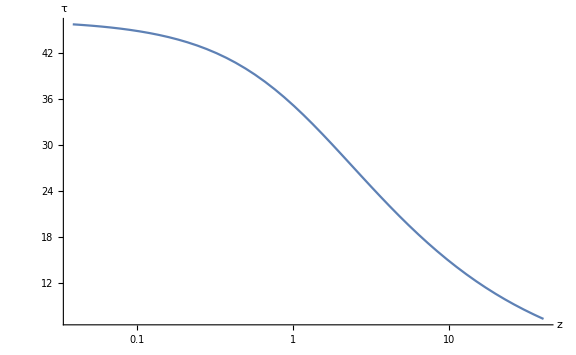

```mathematica
(* Cosmology setting *)
Ωd=0.687;H0=0.0691023;Ωm=0.31;Ωr=9 10^-5; w=-1;
LogLinearPlot[tau[z,H0,Ωm,Ωd,w,Ωr],{z,0,40},ImageSize->Large,PlotRange->All,AxesLabel->{"z","τ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]//pdConv
```

H0 √(Ωd (z+1)^(3 w+1)+Ωm (z+1)+Ωr (z+1)^2)

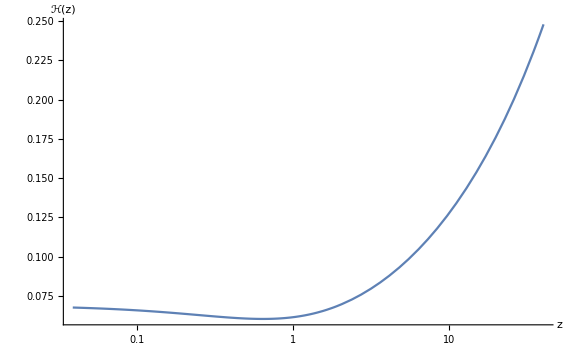

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Eq=ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1;
LogLinearPlot[Eq,{z,0,40},ImageSize->Large,PlotRange->All,AxesLabel->{"z","ℋ(z)"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr]//pdConv
```

-1/2 H0^2 (z+1) ((3 w+1) Ωd (z+1)^(3 w)+Ωm+2 Ωr (z+1))

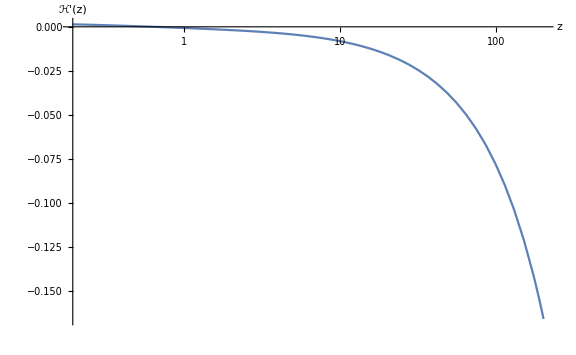

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Eq=ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1;
LogLinearPlot[Eq,{z,0,200},ImageSize->Large,PlotRange->All,AxesLabel->{"z","ℋ'(z)"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

The formula for Ψ

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Sol = DSolve[(Psiequation[ψ,NN,H0,Ωm,Ωd,w]==0),ψ[NN], NN];
Print[Sol];
```

{{ψ[NN]→C[1] Hypergeometric2F1[1/2-1/(2 w),-1/(3 w),1-5/(6 w),-((ⅇ^-NN)^(3 w) Ωd)/Ωm]+((ⅇ^-NN)^(3 w))^(5/6/w) Ωd^(5/6/w) Ωm^(-5/6/w) C[2] Hypergeometric2F1[1/2+1/(3 w),1/(2 w),1+5/(6 w),-((ⅇ^-NN)^(3 w) Ωd)/Ωm]}}

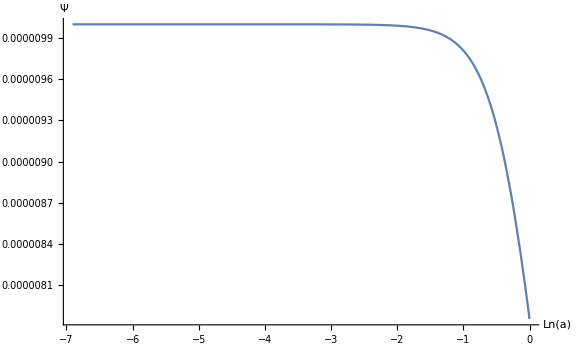

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Plot[ψ[NN]/.Sol/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1/.C[1]->10^-5/.C[2]->0,{NN,Log[1/(1+1000)],Log[1/(1+0)]},ImageSize->Large,PlotRange->All,AxesLabel->{"Ln(a)","Ψ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

Numerical solution of Ψ

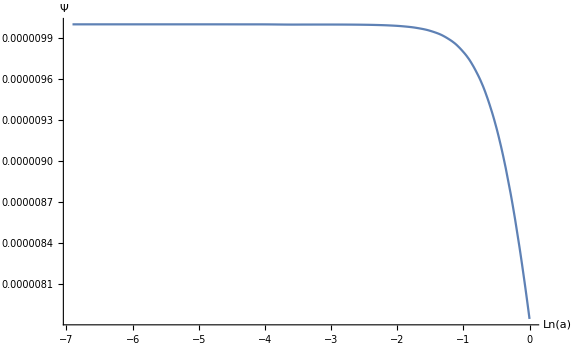

```mathematica
Solnumer = NDSolve[{(Psiequation[ψ,NN,H0,Ωm,Ωd,w]==0)/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1,ψ[Log[1/(1+1000)]]==10^-5,ψ'[Log[1/(1+1000)]]==0},ψ,{NN,Log[1/(1+1000)],Log[1/(1+0)]}];
Plot[ψ[NN]/.Solnumer,{NN,Log[1/(1+1000)],Log[1/(1+0)]},ImageSize->Large,PlotRange->All,AxesLabel->{"Ln(a)","Ψ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

Checking whether at high z (early times) H(τ) behaves like 2/τ as expected

```mathematica
Ωm= 3/10;ΩR = 0;w=-1;H0= 0.06927345697102467;
s = NDSolve[{(a'[tau] -a[tau]H0 √(ΩR a[tau]^-2 + Ωm a[tau]^-1+(1-Ωm)a[tau]^(-(1+3 w)))== 0),a[46]==1},a, {tau,0.01,46.3},Method->"ExplicitRungeKutta"]
```

{{a→InterpolatingFunction[…]}}

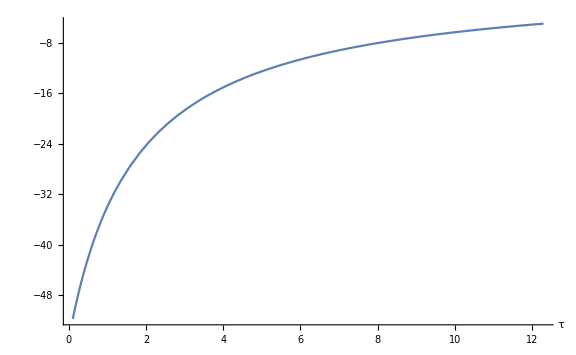

```mathematica
Plot[Evaluate[((a'[t]/.s)/(a[t]/.s))*(t-47)],{t,0.1,12.3},ImageSize->Large,PlotRange->All,AxesLabel->{"τ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

```mathematica
Ωm= 1;ΩR = 0;w=-1;H0= 0.06927345697102467;
s = NDSolve[{(a'[tau] -a[tau]^(-1/2)== 0),a[16]==1},a, {tau,0.0,12.3}]
```

{{a→InterpolatingFunction[…]}}

```mathematica
Ωm= 1;ΩR = 0;w=-1;H0= 0.06927345697102467;
news = NDSolve[{(a'[tau] -a[tau]^(-1/2)== 0),a[47]==1},a, {tau,0.0,46.3}]
```

{{a→InterpolatingFunction[…]}}

## Solutions of the coupled ODEs

Here we use the equations we obtained in the previous section

```mathematica
Clear[Eq,assum,pde];
```

#### PDE and assumptions

```mathematica
Ψ[τ_,x_]:=ψ0[τ]+ψ1[τ] x + ψ2[τ] x^2+ψ3[τ] x^3+ ψ4[τ] x^4;
assum[t_,x_] := Subscript[u, 0][t]+ Subscript[u, 1][t]x +  Subscript[u, 2][t] x^2+Subscript[u, 3][t] x^3+Subscript[u, 4][t] x^4;
L[τ_,x_] := Subscript[l, πd][τ]D[pi[τ,x], τ] + Subscript[l, ππ][τ]pi[τ,x]+Subscript[l, Ψ][τ] Ψ[τ,x]+Subscript[l, Ψd][τ] D[Ψ[τ,x], τ]+Subscript[l, πpp][τ]D[pi[τ,x], x,x];
NonLin[τ_,x_]:= Subscript[ν, πpπp][τ] (D[pi[τ,x], x])^2 +Subscript[ν, πpπpd][τ]D[pi[τ,x], x]D[pi[τ,x], τ,x] + 
Subscript[ν, ππpp][τ] pi[τ,x]D[pi[τ,x], x,x]+Subscript[ν, πdπpp][τ] D[pi[τ,x], τ] D[pi[τ,x], x,x]+
Subscript[ν, Ψπpp][τ] Ψ[τ,x] D[pi[τ,x], x,x]+Subscript[ν, Ψpπp][τ] D[Ψ[τ,x], x]D[pi[τ,x], x]+Subscript[ν, πpπpπpp][τ](D[pi[τ,x], x])^2 D[pi[τ,x], x,x];
Eq[t_,x_]:= D[pi[t,x], t,t]+1*L[t,x]-NonLin[t,x];
```

#### Print the equation

```mathematica
Print[Eq[τ,x]//pdConv]
```

-ν_πpπpd(τ) (∂pi(τ,x))/(∂x) (∂^2 pi(τ,x))/(∂τ ∂x)+l_πpp(τ) (∂^2 pi(τ,x))/(∂x^2)+l_πd(τ) (∂pi(τ,x))/(∂τ)+l_ππ(τ) pi(τ,x)-ν_πdπpp(τ) (∂pi(τ,x))/(∂τ) (∂^2 pi(τ,x))/(∂x^2)-ν_ππpp(τ) pi(τ,x) (∂^2 pi(τ,x))/(∂x^2)-ν_πpπpπpp(τ) (∂^2 pi(τ,x))/(∂x^2) ((∂pi(τ,x))/(∂x))^2-ν_Ψpπp(τ) (∂pi(τ,x))/(∂x) (4 x^3 ψ4(τ)+3 x^2 ψ1(τ) ψ2(τ)+3 x^2 ψ3(τ))-ν_Ψπpp(τ) (∂^2 pi(τ,x))/(∂x^2) (ψ0(τ)+x^4 ψ4(τ)+x^3 ψ1(τ) ψ2(τ)+x^3 ψ3(τ))-ν_πpπp(τ) ((∂pi(τ,x))/(∂x))^2+(∂^2 pi(τ,x))/(∂τ^2)+l_Ψ(τ) (ψ0(τ)+x^4 ψ4(τ)+x^3 ψ1(τ) ψ2(τ)+x^3 ψ3(τ))+l_Ψd(τ) ((∂ψ0(τ))/(∂τ)+x^4 (∂ψ4(τ))/(∂τ)+x^3 ψ1(τ) (∂ψ2(τ))/(∂τ)+x^3 ψ2(τ) (∂ψ1(τ))/(∂τ)+x^3 (∂ψ3(τ))/(∂τ))

```mathematica
NewEq=Block[{pi},pi[τ_,x_]:=assum[τ,x];Eq[τ,x]]
```

(ψ0[τ]+x^3 ψ1[τ] ψ2[τ]+x^3 ψ3[τ]+x^4 ψ4[τ]) l_Ψ[τ]+l_πpp[τ] (2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ])+l_ππ[τ] (u_0[τ]+x u_1[τ]+x^2 u_2[τ]+x^3 u_3[τ]+x^4 u_4[τ])-(u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ])^2 ν_πpπp[τ]-(2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) (u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ])^2 ν_πpπpπpp[τ]-(2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) (u_0[τ]+x u_1[τ]+x^2 u_2[τ]+x^3 u_3[τ]+x^4 u_4[τ]) ν_ππpp[τ]-(3 x^2 ψ1[τ] ψ2[τ]+3 x^2 ψ3[τ]+4 x^3 ψ4[τ]) (u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ]) ν_Ψpπp[τ]-(ψ0[τ]+x^3 ψ1[τ] ψ2[τ]+x^3 ψ3[τ]+x^4 ψ4[τ]) (2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) ν_Ψπpp[τ]+l_Ψd[τ] (ψ0'[τ]+x^3 ψ2[τ] ψ1'[τ]+x^3 ψ1[τ] ψ2'[τ]+x^3 ψ3'[τ]+x^4 ψ4'[τ])-(u_1[τ]+2 x u_2[τ]+3 x^2 u_3[τ]+4 x^3 u_4[τ]) ν_πpπpd[τ] (u_1'[τ]+2 x u_2'[τ]+3 x^2 u_3'[τ]+4 x^3 u_4'[τ])+l_πd[τ] (u_0'[τ]+x u_1'[τ]+x^2 u_2'[τ]+x^3 u_3'[τ]+x^4 u_4'[τ])-(2 u_2[τ]+6 x u_3[τ]+12 x^2 u_4[τ]) ν_πdπpp[τ] (u_0'[τ]+x u_1'[τ]+x^2 u_2'[τ]+x^3 u_3'[τ]+x^4 u_4'[τ])+u_0''[τ]+x u_1''[τ]+x^2 u_2''[τ]+x^3 u_3''[τ]+x^4 u_4''[τ]

```mathematica
For[i=0,i<5,i++,If[i==0, Print["x^0:"NewEq /.{x->0}]];If[i!=0,Print[ToString[x^i,StandardForm]<>": ",Coefficient[NewEq,x^i]]]]
```

x^0: (ψ0[τ] l_Ψ[τ]+l_ππ[τ] u_0[τ]+2 l_πpp[τ] u_2[τ]-u_1[τ]^2 ν_πpπp[τ]-2 u_1[τ]^2 u_2[τ] ν_πpπpπpp[τ]-2 u_0[τ] u_2[τ] ν_ππpp[τ]-2 ψ0[τ] u_2[τ] ν_Ψπpp[τ]+l_Ψd[τ] ψ0'[τ]+l_πd[τ] u_0'[τ]-2 u_2[τ] ν_πdπpp[τ] u_0'[τ]-u_1[τ] ν_πpπpd[τ] u_1'[τ]+u_0''[τ])

x: l_ππ[τ] u_1[τ]+6 l_πpp[τ] u_3[τ]-4 u_1[τ] u_2[τ] ν_πpπp[τ]-8 u_1[τ] u_2[τ]^2 ν_πpπpπpp[τ]-6 u_1[τ]^2 u_3[τ] ν_πpπpπpp[τ]-2 u_1[τ] u_2[τ] ν_ππpp[τ]-6 u_0[τ] u_3[τ] ν_ππpp[τ]-6 ψ0[τ] u_3[τ] ν_Ψπpp[τ]-6 u_3[τ] ν_πdπpp[τ] u_0'[τ]+l_πd[τ] u_1'[τ]-2 u_2[τ] ν_πdπpp[τ] u_1'[τ]-2 u_2[τ] ν_πpπpd[τ] u_1'[τ]-2 u_1[τ] ν_πpπpd[τ] u_2'[τ]+u_1''[τ]

x^2: l_ππ[τ] u_2[τ]+12 l_πpp[τ] u_4[τ]-4 u_2[τ]^2 ν_πpπp[τ]-6 u_1[τ] u_3[τ] ν_πpπp[τ]-8 u_2[τ]^3 ν_πpπpπpp[τ]-36 u_1[τ] u_2[τ] u_3[τ] ν_πpπpπpp[τ]-12 u_1[τ]^2 u_4[τ] ν_πpπpπpp[τ]-2 u_2[τ]^2 ν_ππpp[τ]-6 u_1[τ] u_3[τ] ν_ππpp[τ]-12 u_0[τ] u_4[τ] ν_ππpp[τ]-3 ψ1[τ] ψ2[τ] u_1[τ] ν_Ψpπp[τ]-3 ψ3[τ] u_1[τ] ν_Ψpπp[τ]-12 ψ0[τ] u_4[τ] ν_Ψπpp[τ]-12 u_4[τ] ν_πdπpp[τ] u_0'[τ]-6 u_3[τ] ν_πdπpp[τ] u_1'[τ]-3 u_3[τ] ν_πpπpd[τ] u_1'[τ]+l_πd[τ] u_2'[τ]-2 u_2[τ] ν_πdπpp[τ] u_2'[τ]-4 u_2[τ] ν_πpπpd[τ] u_2'[τ]-3 u_1[τ] ν_πpπpd[τ] u_3'[τ]+u_2''[τ]

x^3: ψ1[τ] ψ2[τ] l_Ψ[τ]+ψ3[τ] l_Ψ[τ]+l_ππ[τ] u_3[τ]-12 u_2[τ] u_3[τ] ν_πpπp[τ]-8 u_1[τ] u_4[τ] ν_πpπp[τ]-48 u_2[τ]^2 u_3[τ] ν_πpπpπpp[τ]-36 u_1[τ] u_3[τ]^2 ν_πpπpπpp[τ]-64 u_1[τ] u_2[τ] u_4[τ] ν_πpπpπpp[τ]-8 u_2[τ] u_3[τ] ν_ππpp[τ]-12 u_1[τ] u_4[τ] ν_ππpp[τ]-4 ψ4[τ] u_1[τ] ν_Ψpπp[τ]-6 ψ1[τ] ψ2[τ] u_2[τ] ν_Ψpπp[τ]-6 ψ3[τ] u_2[τ] ν_Ψpπp[τ]-2 ψ1[τ] ψ2[τ] u_2[τ] ν_Ψπpp[τ]-2 ψ3[τ] u_2[τ] ν_Ψπpp[τ]+ψ2[τ] l_Ψd[τ] ψ1'[τ]+ψ1[τ] l_Ψd[τ] ψ2'[τ]+l_Ψd[τ] ψ3'[τ]-12 u_4[τ] ν_πdπpp[τ] u_1'[τ]-4 u_4[τ] ν_πpπpd[τ] u_1'[τ]-6 u_3[τ] ν_πdπpp[τ] u_2'[τ]-6 u_3[τ] ν_πpπpd[τ] u_2'[τ]+l_πd[τ] u_3'[τ]-2 u_2[τ] ν_πdπpp[τ] u_3'[τ]-6 u_2[τ] ν_πpπpd[τ] u_3'[τ]-4 u_1[τ] ν_πpπpd[τ] u_4'[τ]+u_3''[τ]

x^4: ψ4[τ] l_Ψ[τ]+l_ππ[τ] u_4[τ]-9 u_3[τ]^2 ν_πpπp[τ]-16 u_2[τ] u_4[τ] ν_πpπp[τ]-90 u_2[τ] u_3[τ]^2 ν_πpπpπpp[τ]-80 u_2[τ]^2 u_4[τ] ν_πpπpπpp[τ]-120 u_1[τ] u_3[τ] u_4[τ] ν_πpπpπpp[τ]-6 u_3[τ]^2 ν_ππpp[τ]-14 u_2[τ] u_4[τ] ν_ππpp[τ]-8 ψ4[τ] u_2[τ] ν_Ψpπp[τ]-9 ψ1[τ] ψ2[τ] u_3[τ] ν_Ψpπp[τ]-9 ψ3[τ] u_3[τ] ν_Ψpπp[τ]-2 ψ4[τ] u_2[τ] ν_Ψπpp[τ]-6 ψ1[τ] ψ2[τ] u_3[τ] ν_Ψπpp[τ]-6 ψ3[τ] u_3[τ] ν_Ψπpp[τ]+l_Ψd[τ] ψ4'[τ]-12 u_4[τ] ν_πdπpp[τ] u_2'[τ]-8 u_4[τ] ν_πpπpd[τ] u_2'[τ]-6 u_3[τ] ν_πdπpp[τ] u_3'[τ]-9 u_3[τ] ν_πpπpd[τ] u_3'[τ]+l_πd[τ] u_4'[τ]-2 u_2[τ] ν_πdπpp[τ] u_4'[τ]-8 u_2[τ] ν_πpπpd[τ] u_4'[τ]+u_4''[τ]